```mathematica
{vals, vects}=Eigensystem[m={{2Subscript[ϵ,1]+U,-Sqrt[2]J,0},{-Sqrt[2]J,Subscript[ϵ,1]+Subscript[ϵ,1],-Sqrt[2]J},{0,-Sqrt[2]J,2Subscript[ϵ,1]+U}}];
P=Transpose[vects];
"Diagonalized Hamiltonian. The diagonal elements correspond to the Eigenergies."
FullSimplify[Inverse[P].m.P/.Subscript[ϵ,2]->Subscript[ϵ,1]]//MatrixForm
"Eigenstates"
FullSimplify[P]//MatrixForm
```

Diagonalized Hamiltonian. The diagonal elements correspond to the Eigenergies.

(U+2 ϵ_1 | 0 | 0
0 | 1/2 (U-√(16 J^2+U^2)+4 ϵ_1) | 0
0 | 0 | 1/2 (U+√(16 J^2+U^2)+4 ϵ_1))

Eigenstates

(-1 | 1 | 1
0 | (U+√(16 J^2+U^2))/(2 √2 J) | (U-√(16 J^2+U^2))/(2 √2 J)
1 | 1 | 1)

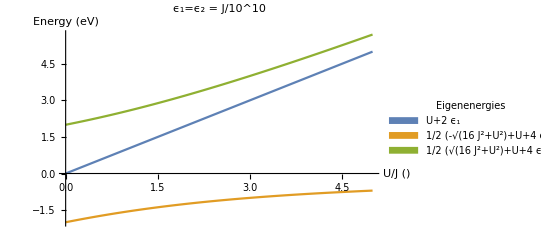

```mathematica
P=Transpose[vects];

FullSimplify[vals];
P//MatrixForm;
P[[All,1]];

ex1 = vals[[1]];
exp1 = vals[[1]]/.Subscript[ϵ,1]->J/10^10/.Subscript[ϵ,2]->J/10^10/. J->1;
f1[U_] := Evaluate[exp1];

ex2 = vals[[2]];
exp2 = vals[[2]]/.Subscript[ϵ,1]->J/10^10/.Subscript[ϵ,2]->J/10^10/. J->1;
f2[U_] := Evaluate[exp2];

ex3 = vals[[3]];
exp3 = vals[[3]]/.Subscript[ϵ,1]->J/10^10/.Subscript[ϵ,2]->J/10^10/. J->1;
exp3;
f3[U_] := Evaluate[exp3];

Plot[{f1[U], f2[U], f3[U]},{U,0,5},
PlotLegends->{SwatchLegend[{FullSimplify[ex1],FullSimplify[ex2], FullSimplify[ex3]},LegendLabel->"Eigenenergies"]}, AxesLabel->{Style["U/J ()",16],Style["Energy (eV)",16]}, Ticks->None,
PlotLabel->Style[ToString[Subscript[ϵ,1], StandardForm]<>"="<>ToString[Subscript[ϵ,2], StandardForm]<>" = J/10^10", FontSize->18]]
```

```mathematica
N[f2[10000000]]
```

0.2

```mathematica
{vals, vects}=Eigensystem[m={{Subscript[ϵ,1],-J},{-J,Subscript[ϵ,2]}}];
m//MatrixForm;
P=Transpose[vects];
"Diagonalized Hamiltonian. The diagonal elements correspond to the Eigenergies."
FullSimplify[Inverse[P].m.P]//MatrixForm
"Eigenstates"
FullSimplify[P]//MatrixForm
```

Diagonalized Hamiltonian. The diagonal elements correspond to the Eigenergies.

(1/2 (ϵ_1-√(4 J^2+(ϵ_1-ϵ_2)^2)+ϵ_2) | 0
0 | 1/2 (ϵ_1+√(4 J^2+(ϵ_1-ϵ_2)^2)+ϵ_2))

Eigenstates

((-ϵ_1+√(4 J^2+(ϵ_1-ϵ_2)^2)+ϵ_2)/(2 J) | -(ϵ_1+√(4 J^2+(ϵ_1-ϵ_2)^2)-ϵ_2)/(2 J)
1 | 1)

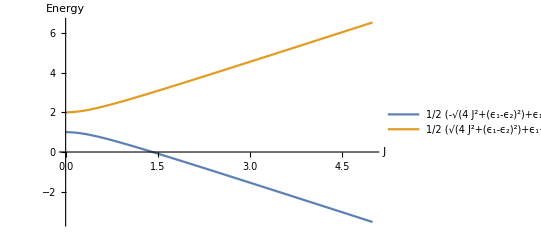

```mathematica
"Equal";
FullSimplify[vals/.Subscript[ϵ,1]->1/.Subscript[ϵ,2]->1];
P/.Subscript[ϵ,1]->1/.Subscript[ϵ,2]->1//MatrixForm;
"e1<e2";
FullSimplify[vals]/.Subscript[ϵ,1]->1/.Subscript[ϵ,2]->2;
P/.Subscript[ϵ,1]->1/.Subscript[ϵ,2]->2//MatrixForm;
"e1>e2";
FullSimplify[vals]/.Subscript[ϵ,1]->2/.Subscript[ϵ,2]->1;
P/.Subscript[ϵ,1]->2/.Subscript[ϵ,2]->1//MatrixForm;

exp1 = vals[[1]];
exp1;
g1[J_] := Evaluate[exp1];

exp2 = vals[[2]];
exp2;
g2[J_] := Evaluate[exp2];

Plot[{g1[J]/.Subscript[ϵ,1]->2/.Subscript[ϵ,2]->1, g2[J]/.Subscript[ϵ,1]->2/.Subscript[ϵ,2]->1},{J,0,5},
PlotLegends->{FullSimplify[exp1],FullSimplify[exp2]},
AxesLabel->{Style["J",16],Style["Energy",16]}, Ticks->None]
```